{0,11.25,13,15,17,19,23,25,29,31,33,39,49}

test

{{0,0},{14,11.25},{18.38,13},{27,15},{38,17},{46,19},{64,23},{71,25},{84,29},{89,31},{91,33},{104,39},{115,49}}

1.0629+0.768114 x-0.0110443 x^2+0.0000695113 x^3

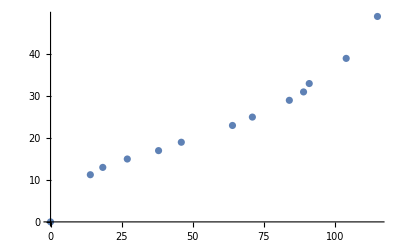

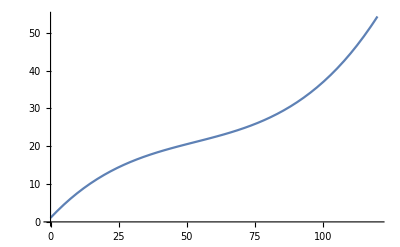

```mathematica
data={{-9,0},{2.25,14},{4,18.38},{6,27},{8,38},{10,46},{14,64},{16,71},{20,84},{22,89},{24,91},{30,104},{40,115}};
data[[All,1]]+=9
Print["test"]
data=Reverse/@data
n=3;
bestFit=Fit[data,Table[x^k,{k,0,n}],x]
ListPlot[data,PlotRange->All]
Plot[{bestFit},{x,0,120}]
```